```mathematica
(*Define the function G*)G[a_,b_,c_,d_]:=a/(b-c/d)-a/(b+c/d)
Manipulate[Module[{sol,AC,ACp,PDE,PDEp,cAMP,t},sol=NDSolve[{ACp'[t]==r3*AC[t]*cAMP[t]/(K3+AC[t])-r4*Et*ACp[t]/(K4+ACp[t])+q1-q2*ACp[t],AC'[t]==r4*Et*ACp[t]/(K4+ACp[t])-r3*AC[t]*cAMP[t]/(K3+AC[t])+0*q1-q2/4*AC[t],PDEp'[t]==r1*PDE[t]*cAMP[t]/(K1+PDE[t])-r2*Dt*PDEp[t]/(K2+PDEp[t]),PDE'[t]==r2*Dt*PDEp[t]/(K2+PDEp[t])-r1*PDE[t]*cAMP[t]/(K1+PDE[t]),cAMP'[t]==(k0+k1*ACp[t])-(k3+k4*PDEp[t])*cAMP[t],AC[0]==x0[[1]],ACp[0]==x0[[2]],PDE[0]==x0[[3]],PDEp[0]==x0[[4]],cAMP[0]==x0[[5]]},{AC,ACp,PDE,PDEp,cAMP},{t,0,500}];
Plot[Evaluate[{PDEp[t],cAMP[t]}/. sol],{t,0,500},PlotRange->All,PlotLegends->{"PDEp(t)","cAMP(t)"},AxesLabel->{"Time","Concentration"}]],
{{k0,0},0,10,Appearance->"Labeled"},
{{k1,2.85},0,10,Appearance->"Labeled"},
{{k3,0.69},0,10,Appearance->"Labeled"},
{{k4,4.45},0,10,Appearance->"Labeled"},
{{r1,0.52},0,10,Appearance->"Labeled"},
{{r2,0.47},0,10,Appearance->"Labeled"},
{{r3,2},0,10,Appearance->"Labeled"},
{{r4,10},0,10,Appearance->"Labeled"},
{{Et,0.28},0,10,Appearance->"Labeled"},
{{Dt,0.15},0,10,Appearance->"Labeled"},
{{K1,0.1},0,10,Appearance->"Labeled"},
{{K2,0.1},0,10,Appearance->"Labeled"},
{{K3,0.001},0,10,Appearance->"Labeled"},
{{K4,1},0,10,Appearance->"Labeled"},
{{q1,0},0,10,Appearance->"Labeled"},
{{q2,0},0,10,Appearance->"Labeled"},{{x0,{0.33,0.33,0.33,0.33,0.33}},Appearance->"Labeled"},Button["Randomize Parameters",k0=RandomReal[{-10,10}];
k1=RandomReal[{0,10}];
k3=RandomReal[{0,10}];
k4=RandomReal[{0,10}];
r1=RandomReal[{0,10}];
r2=RandomReal[{0,10}];
r3=RandomReal[{0,10}];
r4=RandomReal[{0,10}];
Et=RandomReal[{0,10}];
Dt=RandomReal[{0,10}];
K1=RandomReal[{0,10}];
K2=RandomReal[{0,10}];
K3=RandomReal[{0,10}];
K4=RandomReal[{0,10}];
q1=RandomReal[{0,10}];
q2=RandomReal[{0,10}]],TrackedSymbols->{k0,k1,k3,k4,r1,r2,r3,r4,Et,Dt,K1,K2,K3,K4,q1,q2,x0}
]
```

```mathematica
k0 = 0
k1 = 2.85
k3 = 0.69
k4 = 4.45
r1 = 0.52
r2=0.47
r3 = 2
r4 = 10
Et = 0.28
Dt = 0.15
K1 = 0.1
K2 = 0.1
K3 = 0.001
K4 = 1
q1 = 0
q2 = 0
{0.33,0.33,0.33,0.33,0.33}
```

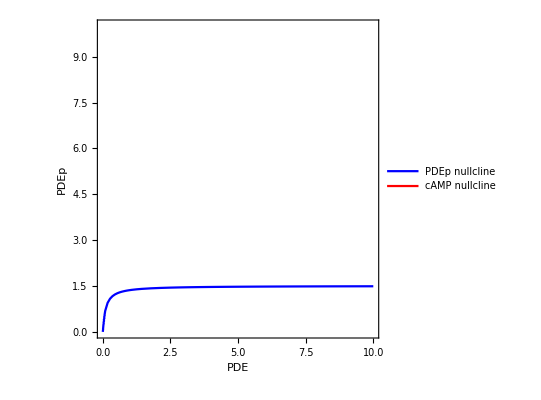

```mathematica
k0=0;
k1=2.85;
k3=0.69;
k4=4.45;
r1=0.52;
r2=0.47;
r3=2;
r4=10;
Et=0.28;
DTOTAL=0.15;
K1=0.1;
K2=0.1;
K3=0.001;
K4=1;
q1=0;
q2=0;
ACp=0.33;

sol=Solve[{r1*PDE*cAMP/(K1+PDE)-r2*DTOTAL*PDEp/(K2+PDEp)==0//Rationalize,(k0+k1*ACp)-(k3+k4*PDEp)*cAMP==0//Rationalize},{cAMP,PDEp}];

nullclinePDEp=PDEp/. sol[[1]]//N;
nullclinecAMP=cAMP/. sol[[2]]//N;

ContourPlot[{Evaluate[nullclinePDEp==PDEp],Evaluate[nullclinecAMP==cAMP]},{PDE,0,10},{PDEp,0,10},ContourStyle->{Blue,Red},FrameLabel->{"PDE","PDEp"},PlotLegends->{"PDEp nullcline","cAMP nullcline"},BaseStyle->{FontFamily->"Arial",FontSize->12}]
```